28200000/543169

The central frequency is 407.056 THz

The frequency bandwidth is 51.9175 THz

-Graphics-

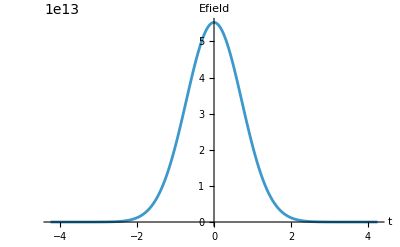

```mathematica
(* parameters*)
ClearAll["Global`*"]

λ = 737*10^(-9); (*m*)
fo = (3*10^(8)/λ)*10^(-12); (*THz*)
ωo = 2*Pi*fo*10^(12); (*rad/s*)
Δλ = 94*10^(-9);  (*m*)
Δf= ((3*10^8)/λ^2*Δλ)*10^(-12) (*Thz*)
Δω = 2*Pi*Δf*10^(12);
Δt = .441/(Δf*10^(12)); (*s*)

A = 1;

tmin=-5*Δt;
tmax=5*Δt;
tmin1=-5*Δt;
tmax1=5*Δt;
ωmin = -5*Δω+ωo;
ωmax = 5*Δω+ωo;

σt = Δt/(2*√(2*Log[2]));
σω = Δω/(2*√(2*Log[2]));

Print["The central frequency is ", N[fo], " THz"]
Print["The frequency bandwidth is ", N[Δf], " THz"]

(* E field in the frequency domain*)
Efieldω[ω_] := A* Exp[-(ω-ωo)^2/(2σω^2)];

(*E field in the time domain Fourier transformed from the frequency domain*)
Efieldt[t_] =∫_(-∞)^∞ (1/(2Pi))Efieldω[w]Exp[-I*w*t]ⅆw;

Plot[Efieldω[ω],{ω,ωmin,ωmax},PlotPoints->500,MaxRecursion->4,PlotRange->All, AxesLabel->{ω, Efield}]
Plot[Abs[Efieldt[t]], {t, tmin1, tmax1}, PlotPoints->500, MaxRecursion->4, PlotRange->All, AxesLabel->{t, Efield}]
```

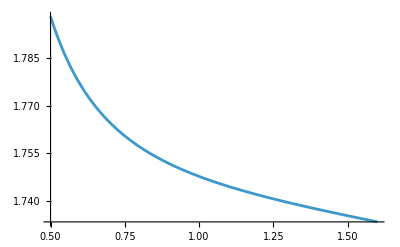

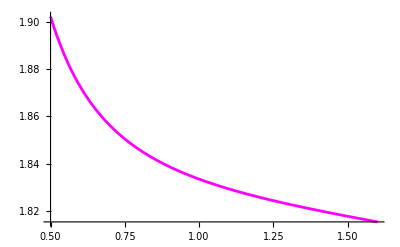

```mathematica
(*Sellemeier Equations for PPKTP*)
(*z axis: https://doi.org/10.1063/1.123408*)(*y axis: https://doi.org/10.1063/1.1668320*)
(*temperature dependence: https://opg.optica.org/ao/fulltext.cfm?uri=ao-42-33-6661*)

(*y*)
A1y = 2.09930;
A2y = 0.922683;
A3y = 0.0467695;
A4y = 0.0138408;

(*z*)
Az = 2.12725;
Bz = 1.18431;
Cz = 5.14852*10^-2;
Dz = 0.6603;
Ez = 100.00507;
Fz = 9.68956*10^-3;

temp = 60;

n1z[λ_] := 9.9587*10^-6 + 9.9228*10^-6/λ + -8.9603*10^-6/(λ^2) + 4.1010*10^-6/(λ^3);
n2z[λ_] := -1.1882*10^-8 + 10.459*10^-8/λ + -9.8136*10^-8/(λ^2) + 3.1481*10^-8/(λ^3);
Δnz[λ_] := n1z[λ]*(temp-25) +n2z[λ]*(temp-25)^2;

n1y[λ_] := 6.2897*10^-6+ 6.3061*10^-6/λ + -6.0629*10^-6/(λ^2) + 2.6486*10^-6/(λ^3);
n2y[λ_] := -.14445*10^-8+ 2.2244*10^-8/λ + -3.5770*10^-8/(λ^2) + 1.3470*10^-8/(λ^3);
Δny[λ_] := n1y[λ]*(temp-25) +n2y[λ]*(temp-25)^2;

ny[λ_] :=Sqrt[A1y + A2y/(1-A3y/(λ^2)) -A4y*λ^2] +Δny[λ];

nz[λ_] :=Sqrt[Az + Bz/(1-Cz/(λ^2)) + Dz/(1-Ez/(λ^2))-Fz*λ^2] + Δnz[λ];

p1 = Plot[ny[λ], {λ, 0.5, 1.6}]
p2 = Plot[nz[λ], {λ, 0.5, 1.6}, PlotStyle->Magenta]
```

```mathematica
λpo = 520*10^-9; 
λso = 780*10^-9; 
λio = 1/(1/λpo -1/λso);
c = 3*10^8;

Print["The central wavelength for the idler is ", N[λio], " nm"]

ωpo = 2π c/λpo;
ωso = 2π c/λso;
ωio = 2π c/λio;

kpo = nz[λpo*10^6]*ωpo/c;
kso = nz[λso*10^6]*ωso/c;
kio = nz[λio*10^6]*ωio/c;

Λ = (-2π/(-kpo + kso +kio))*10^6;
Print["The poling period is ", N[Λ], " microns"]
```

The central wavelength for the idler is 1.56×10^-6 nm

The poling period is 9.05838 microns

```mathematica
Clear[λi, λs];

Δt=1*10^-9;
Δν=(.441/Δt) /10^12;
σν=Δν/(2*Sqrt[2*Log[2]]);

λs[ν_]:=c/ν;
λi[ν_]:=c/ν;

L = 1*10^-2;

νso = (c/λso) /10^12;
νio = (c/λio) /10^12;
νpo = (c/λpo) /10^12;

νsmin = νso - .005;
νsmax = νso + .005;
νimin = νio - .005;
νimax = νio + .005;

Print["The central frequency for the signal is ", N[νso], " Thz"];
Print["The central frequency for the idler is ", N[νio], " Thz"];

Δk0 = -nz[λpo*10^6]*2π *νpo/c + nz[λso*10^6]*2π *νso/c + nz[λio*10^6]*2π * νio/c  + 2π/(Λ*10^6) ;
Print["Delta k is ",N[Δk0]]

 (*next order term*)
dkp = D[2π nz[c/νp*10^-6] (νp*10^12/c), νp] /. νp -> νpo;
dks = D[2π nz[c/νs*10^-6] (νs*10^12/c), νs] /. νs -> νso;
dki = D[2π nz[c/νi*10^-6] (νi*10^12/c), νi] /. νi -> νio;
Δk1 = dkp*((νs - νso) + (νi - νio)) - dks*(νs-νso) - dki*(νi - νio);

Δk[ νs_,νi_]:= Δk0  + Δk1  ;
α[νs_, νi_] := A* Exp[-(νi+νs-νpo)^2/(2σν^2)];
ϕ[νs_, νi_] := Sinc[(Δk[νs,νi] *L)/2];

JSA[νs_,νi_] := ϕ[νs,νi]*α[νs, νi];
JSI[νs_, νi_] := JSA[νs,νi]*Conjugate[JSA[νs,νi]];


DensityPlot[α[νs,νi],{νs,νsmin,νsmax},{νi,νimin,νimax}, PlotPoints->100, PlotRange->All, PlotLabel->"Pump",FrameLabel->{"Signal (THz)","idler (Thz)",None,None}]
DensityPlot[ϕ[νs,νi],{νs,νsmin,νsmax},{νi,νimin,νimax}, PlotPoints->100, PlotRange->All, PlotLabel->"Phasematching",FrameLabel->{"Signal (THz)","idler (Thz)",None,None}]
DensityPlot[JSI[νs,νi],{νs,νsmin,νsmax},{νi,νimin,νimax},PlotPoints->100, PlotRange->All, PlotLabel->"JSI",FrameLabel->{"Signal (THz)","idler (Thz)",None,None}]
```

The central frequency for the signal is 384.615 Thz

The central frequency for the idler is 192.308 Thz

Delta k is 1.69407×10^-21

General::munfl: Exp[-1425.58] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

-Graphics-

General::munfl: Exp[-1425.58] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-